```mathematica
Do[

Do[

(*For[d=0.08,d<0.081,d+=0.0002,*)

dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
frt=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frts[l][d]=Table[frt[[i]],{i,1,Length[frt]/(Pi*50)}];

frf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DFree-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frfs[l][d]=Table[frf[[i]],{i,1,Length[frf]/(Pi*50)}];

frbaux=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DBreak-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frb=Table[frbaux[[i]],{i,1,Length[frbaux],2}];

frbs[l][d]=Table[frb[[i]],{i,1,Length[frb]/(Pi*50)}];


,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]
,{l,{5,10,20,30,40,50}}]
```

```mathematica
l=10;
d=0.082;
frts[l][d]
frts[l][d][[1]][[2]]
```

```mathematica
d0=0.0812;
d1=0.105;
ω=0.3825;
ν=1/0.13;
Do[

Do[

ξ[l][d]=Abs[(d-d0-d1*(l*1000)^(-ω))/(d0+d1*(l*1000)^(-ω))]^(-ν);

,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

ξd[l]=Table[{d,ξ[l][d]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];
,{l,{5,10,20,30,40,50,100}}]
```

```mathematica
ξd[5]
```

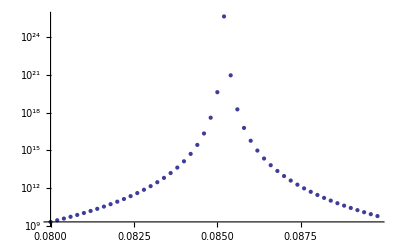

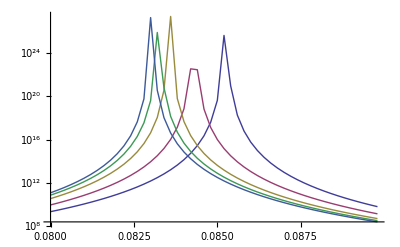

```mathematica
ListLogPlot[{ξd[5]},PlotRange->Full]
ListLogPlot[{ξd[5],ξd[10],ξd[20],ξd[30],ξd[40]},PlotRange->Full,Joined->True]
```

```mathematica
Do[
maxft[l]=Table[{d,frts[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxft2[l]=Table[{d,frts[l][d][[1]][[2]]/(l*1000)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxff[l]=Table[{d,frfs[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxff2[l]=Table[{d,frfs[l][d][[1]][[2]]/(l*1000)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];


maxfb[l]=Table[{d,frbs[l][d][[1]][[2]]},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];

maxfb2[l]=Table[{d,frbs[l][d][[1]][[2]]/(l*1000)^2},{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}];


,{l,{5,10,20,30,40,50,100}}]
```

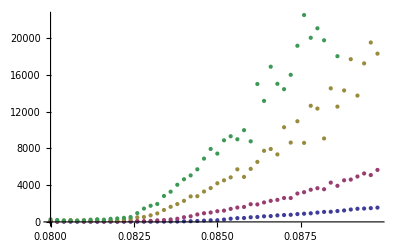

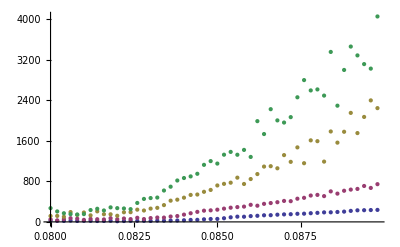

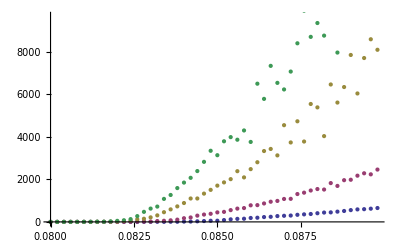

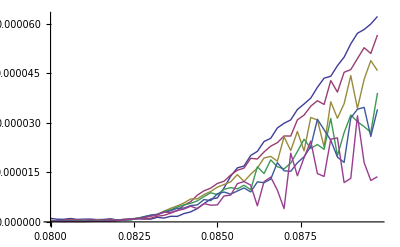

```mathematica
ListPlot[{maxft[5],maxft[10],maxft[20],maxft[30]}]
ListPlot[{maxff[5],maxff[10],maxff[20],maxff[30]}]
ListPlot[{maxfb[5],maxfb[10],maxfb[20],maxfb[30]}]

ListLinePlot[{maxft2[5],maxft2[10],maxft2[20],maxft2[30],maxft2[40],maxft2[50]}]
```

```mathematica
maxfts[5]
```

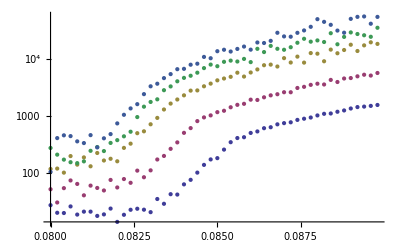

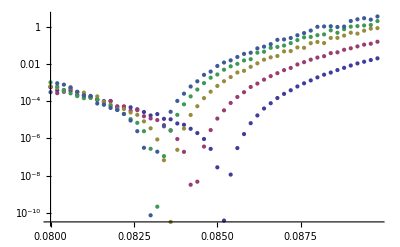

```mathematica
η=1.5;
Do[
maxfts[l]=Table[{maxft[l][[All,1]][[i]],maxft[l][[All,2]][[i]]*ξ[l][maxft[l][[All,1]][[i]]]^(η-2)},{i,1,Length[maxft[l]]}];

maxffs[l]=Table[{maxff[l][[All,1]][[i]],maxff[l][[All,2]][[i]]*ξ[l][maxff[l][[All,1]][[i]]]^(η-2)},{i,1,Length[maxff[l]]}];

maxfbs[l]=Table[{maxfb[l][[All,1]][[i]],maxfb[l][[All,2]][[i]]*ξ[l][maxfb[l][[All,1]][[i]]]^(η-2)},{i,1,Length[maxfb[l]]}];

,{l,{5,10,20,30,40,50,100}}]

ListLogPlot[{maxft[5],maxft[10],maxft[20],maxft[30],maxft[40]},PlotRange->Full]
ListLogPlot[{maxfts[5],maxfts[10],maxfts[20],maxfts[30],maxfts[40]},PlotRange->Full]
```

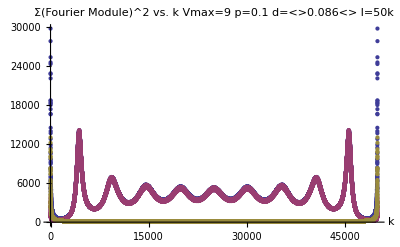

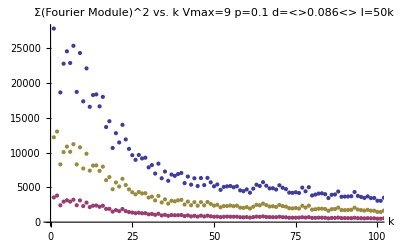

```mathematica
ListPlot[{frt,frf,frb},PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{frt,frf,frb},PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->{{0,100},{0,frt[[All,2]][[1]]}}]
```

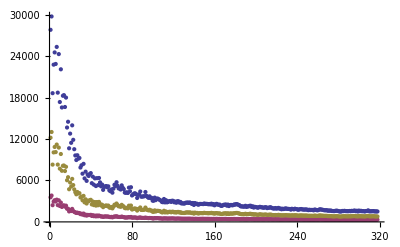

```mathematica
ListPlot[{frts,frfs,frbs},PlotRange->Full]
```

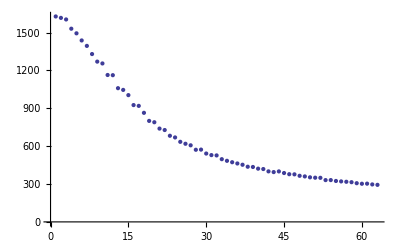

```mathematica
ListPlot[frts[10][0.0858]]
```

```mathematica
η=1.5;
Do[

Do[


FRTS[l][d]=Table[{frts[l][d][[All,1]][[i]]*ξ[l][d],frts[l][d][[All,2]][[i]]* ξ[l][d]^(η-2) },{i,1,Length[frts[l][d]]}];

FRFS[l][d]=Table[{frfs[l][d][[All,1]][[i]]*ξ[l][d],frfs[l][d][[All,2]][[i]]* ξ[l][d]^(η-2) },{i,1,Length[frfs[l][d]]}];

FRBS[l][d]=Table[{frbs[l][d][[All,1]][[i]]*ξ[l][d],frbs[l][d][[All,2]][[i]]* ξ[l][d]^(η-2) },{i,1,Length[frbs[l][d]]}];

,{d,{0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898}}]
,{l,{5,10,20,30,40,50,100}}]
```

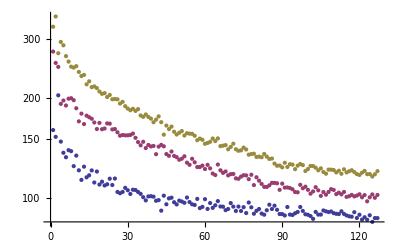

-Graphics-

```mathematica
l=20;
d=0.082;
ListLogPlot[{frts[l][0.082],frts[l][0.0822],frts[l][0.0824]}]
ListLogPlot[{FRTS[l][0.082],FRTS[l][0.0822],FRTS[l][0.0824]}]
```

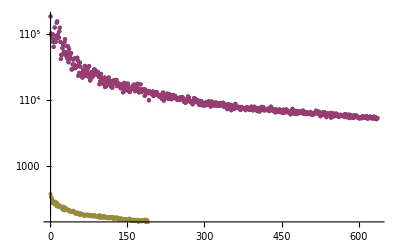

-Graphics-

```mathematica
ListLogPlot[{frts[5][0.082],frts[10][0.082],frts[30][0.082]},PlotRange->Full]
ListLogPlot[{FRTS[5][0.082],FRTS[10][0.082],FRTS[30][0.082]},PlotRange->Full]
```

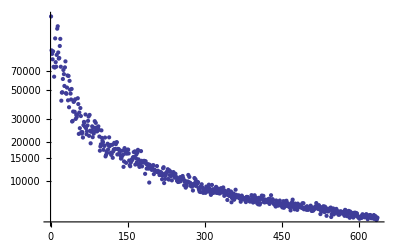

```mathematica
ListLogPlot[{frts[5][0.082]}]
```

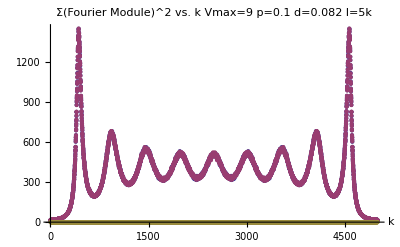

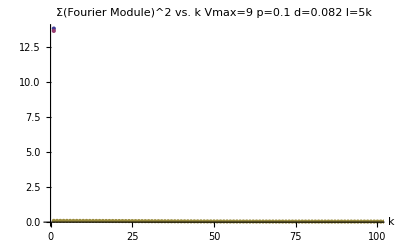

```mathematica
dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
frt=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
frf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DFree-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frbaux=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam2/Fourier1DBreak-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

frb=Table[frbaux[[i]],{i,1,Length[frbaux],2}];

ListPlot[{frt,frf,frb},PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  dd<>" l="<>ll<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{frt,frf,frb},PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  dd<>" l="<>ll<>"k",AxesLabel->{"k"," "},PlotRange->{{0,100},{0,frt[[All,2]][[1]]}}]
```